## Fitting the spectral irradiance curve

```mathematica
h=LinguisticAssistant//UnitConvert//QuantityMagnitude;
c=LinguisticAssistant//UnitConvert//QuantityMagnitude;
k=LinguisticAssistant//UnitConvert//QuantityMagnitude;
r=LinguisticAssistant//UnitConvert//QuantityMagnitude;
rSun=LinguisticAssistant//UnitConvert//QuantityMagnitude;
```

```mathematica
fitData=Import[
"C:\\Users\\bvptr\\academia\\physics\\year2\\natuurkunde_en_sterrenkunde_practicum2\\solar_physics\\data\\to_fit.csv"
]//Transpose;
```

```mathematica
spectrum=Table[10^9 fitData[[2]][[2;;]][[i]],{i,1,Length[fitData[[3]][[2;;]]]}]; (* because spectrum was per nm *)
wavelengths=Table[10^-9 fitData[[3]][[2;;]][[i]],{i,1,Length[fitData[[3]][[2;;]]]}]; (* we want SI Units *)
```

```mathematica
dataCoordPairs={wavelengths, spectrum}//Transpose;
```

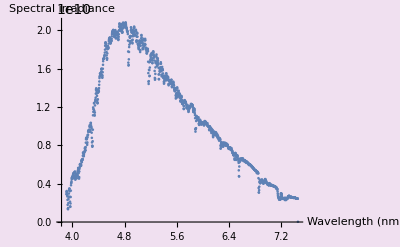

```mathematica
ListPlot[dataCoordPairs,Background->LightPurple, AxesLabel->{"Wavelength (nm", "Spectral irradiance"}]
```

General::munfl: 2.26246×10^31 1.319140923×10^-26831 is too small to represent as a normalized machine number; precision may be lost.

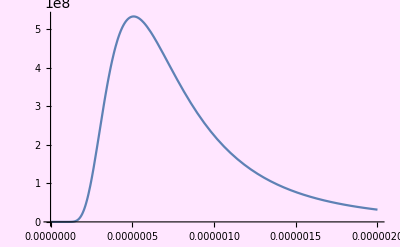

```mathematica
Plot[ (2h c^2)/(λ^5(Exp[h c/(λ k t)]-1))(rSun/r)^2/.t->5700,{λ,0,2000 10^-9},Background->LightMagenta,PlotRange->{{0,2000 10^-9},Automatic}]
```

```mathematica
nlm=NonlinearModelFit[dataCoordPairs, (2h c^2)/(λ^5(Exp[h c/(λ k t)]-1))(rSun/r)^2,{{t,6000}},λ]
```

FittedModel[(2.58×10^-21)/((-1+ⅇ^(1.06964×10^-6/λ)) λ^5)]

```mathematica
nlm["BestFit"]
```

(2.58×10^-21)/((-1+ⅇ^(1.06964×10^-6/λ)) λ^5)

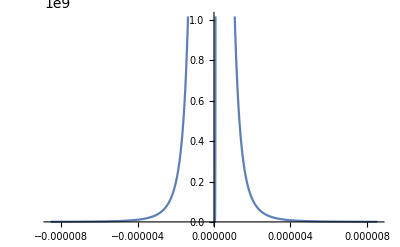

```mathematica
Plot[(2.57584969762645251`3.698965657070013*^-21)/((-1+ⅇ^(1.0696444160064022*^-6/λ)) λ^5),{λ,-8.557155328051217*^-6,8.557155328051217*^-6}]
```

General::munfl: 8.78335×10^51 3.42×10^-11391 is too small to represent as a normalized machine number; precision may be lost.

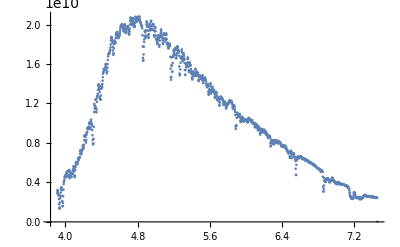

```mathematica
Show[ListPlot[dataCoordPairs],Plot[(nlm["BestFit"])[λ],{λ,0,2000 10^-9}]]
```

### Generating some planck curves

```mathematica
Table[StringForm["`` K", t] ,{t,3500,5500,500}]
```

{3500 K,4000 K,4500 K,5000 K,5500 K}

General::munfl: 8.78335×10^51 1.179859331×10^-43712 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.78335×10^51 1.1812515234×10^-38250 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.78335×10^51 1.972254441×10^-34002 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

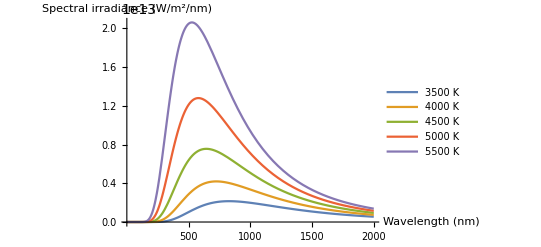

planck.jpg

```mathematica
plot=Plot[Evaluate[Table[ (2h c^2)/(λ^5(Exp[h c/(λ k t)]-1)),{t,3500,5500,500}]],{λ,0,2000 10^-9},Background->White,PlotRange->{{0,2000 10^-9},Automatic},PlotLegends->Table[StringForm["`` K", t] ,{t,3500,5500,500}],AxesLabel->{"Wavelength (nm)","Spectral irradiance (W/m^2/nm)"},Ticks->{Table[{λ 10^-9 ,StringForm["``",λ]}, {λ,500,2000,500}],Automatic}]
Export["planck.jpg",plot]
```